### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={100,500,500}; (*мощности слоев*)
slopes = {0Degree, -0.9 Degree, -0.3 Degree, 2 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

hDispersion = 1000;(*степень складчатости нижнего слоя в метрах*)
hTapering =2; (*степень влияния нижнего горизонта на верхние*)

type = -1 ;
listV = {1500,2000,2300,2500, 2800}; (*набор скоростей!!!больше на 2 чем горизонтов*)
```

```mathematica
velocityTrend = 1;(*1 or 0*)
velocityAnomaly =1; (*1 or 0*)
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "random"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
horizons = BuildDepthSection[listH,slopes,len,dx,hDispersion,hTapering, type][["horizons"]];
table = BuildDepthSection[listH,slopes,len,dx,hDispersion,hTapering, type][["table"]];
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"};
PlotDepthSection[horizons, optsDepth]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]];
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

Dataset[<>]

```mathematica
PlotVelocity[velModel, horizons]
```

-Graphics-

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"};
PlotTimeSection[time, optsTime]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]];
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]];
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section",GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},											
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

```mathematica
|
```

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

{FittedModel[43.3206+2780.82 t],FittedModel[202.288+2504.47 t],FittedModel[559.022+2334.17 t],FittedModel[1453.88+1627.72 t]}

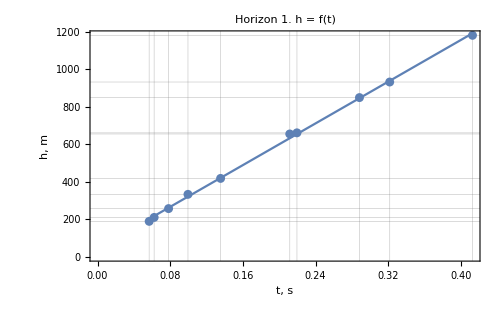
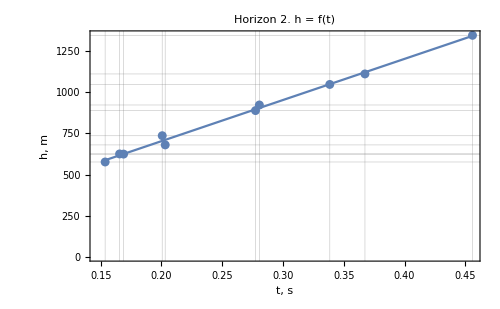
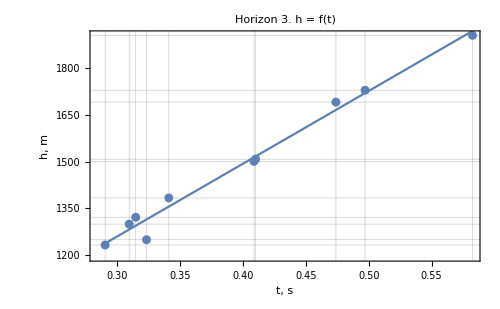
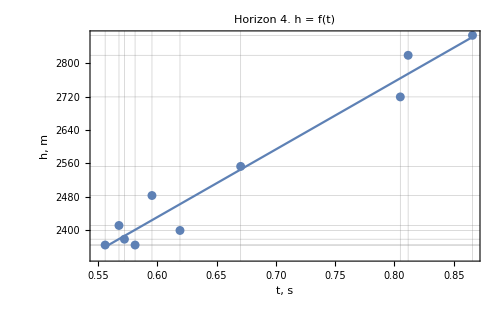

```mathematica
Clear[t];
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]];
PlotHT[wellValuesHT,lmSetHT, t]
```

### VTMethod

{FittedModel[3394.86-1475.47 t],FittedModel[4145.79-2924.22 t],FittedModel[5142.77-3346.08 t],FittedModel[5894.27-3041.68 t]}

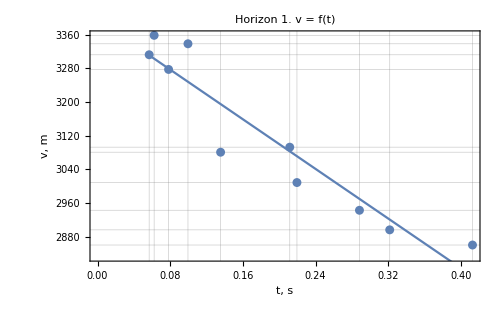
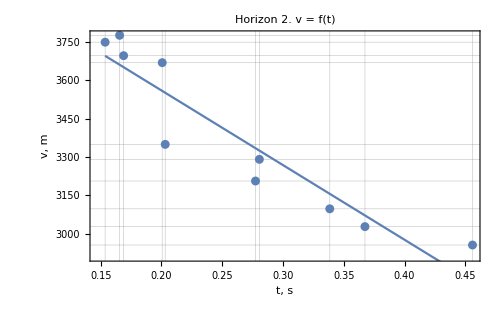
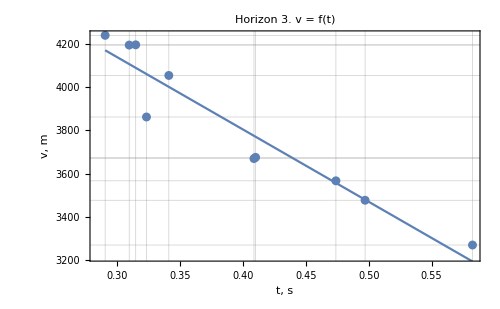
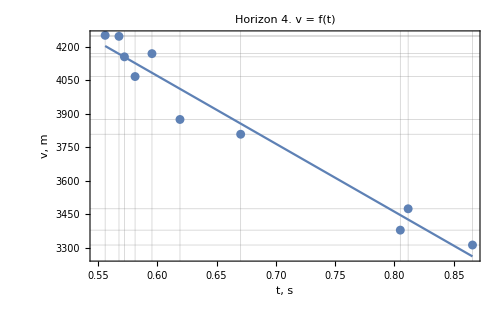

```mathematica
lmSetVT=VTMethod[wellDataset,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,time, t][["lmParametres"]];
wellValuesVT=VTMethod[wellDataset,time, t][["wellValues"]];
resultVT = VTMethod[wellDataset, time, t][["result"]];
fitsVT = VTMethod[wellDataset, time, t][["fits"]];
PlotVT[wellValuesVT,lmSetVT, t]
```

### THMethod

{FittedModel[-0.01536+0.000359221 h],FittedModel[-0.0792184+0.000397474 h],FittedModel[-0.229752+0.000421842 h],FittedModel[-0.830034+0.000589443 h]}

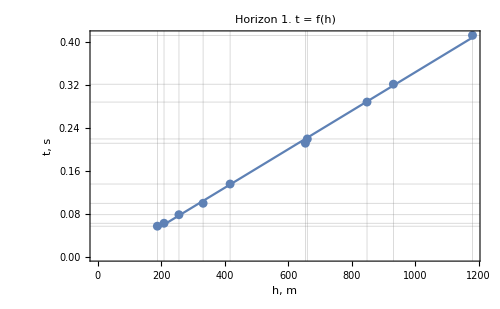
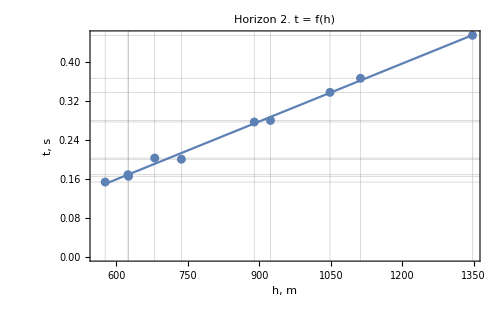
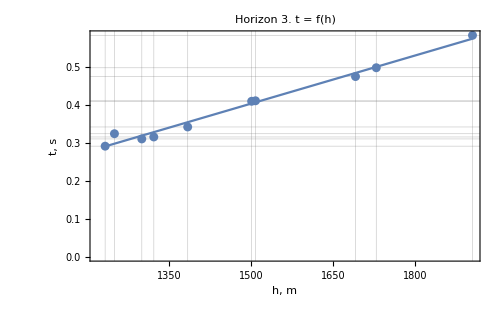
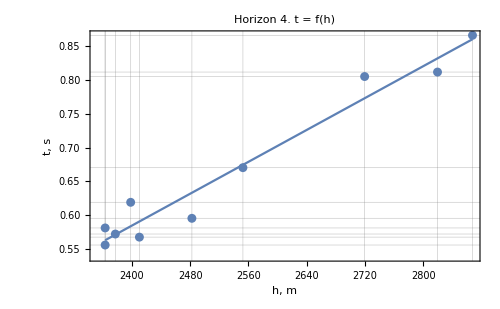

```mathematica
Clear[h];
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]];
resultTH=THMethod[wellDataset, time, h][["result"]];
PlotTH[wellValuesTH,lmSetTH, h]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]];
fitsVave = VaveMethod[wellDataset, time][["fits"]]
```

{3116.52,3382.04,3820.08,3873.25}

{{{0,-1141.74},{100,-789.427},{200,-579.239},{300,-454.426},{400,-392.552},{500,-382.548},{600,-416.772},{700,-495.704},{800,-623.58},{900,-767.955},{1000,-1007.63},{1100,-1103.62},{1200,-1063.93},{1300,-972.679},{1400,-866.077},{1500,-761.185},{1600,-653.527},{1700,-585.63},{1800,-643.804},{1900,-709.218},{2000,-806.627},{2100,-884.072},{2200,-945.936},{2300,-951.347},{2400,-877.044},{2500,-814.437},{2600,-768.531},{2700,-761.184},{2800,-768.941},{2900,-659.51},{3000,-560.961},{3100,-434.739},{3200,-310.324},{3300,-228.962},{3400,-194.09},{3500,-194.327},{3600,-237.511},{3700,-256.697},{3800,-274.942},{3900,-274.343},{4000,-335.004},{4100,-422.298},{4200,-496.834},{4300,-593.629},{4400,-604.332},{4500,-457.929},{4600,-334.121},{4700,-177.279},{4800,-81.0839},{4900,-43.2894},{5000,-100.118},{5100,-173.831},{5200,-243.83},{5300,-386.59},{5400,-467.667},{5500,-566.006},{5600,-684.163},{5700,-708.704},{5800,-785.082},{5900,-893.621},{6000,-922.45},{6100,-913.645},{6200,-938.248},{6300,-970.997},{6400,-1008.89},{6500,-1157.47},{6600,-1286.4},{6700,-1334.37},{6800,-1332.1},{6900,-1289.26},{7000,-1160.21},{7100,-1020.14},{7200,-914.635},{7300,-853.223},{7400,-836.3},{7500,-792.144},{7600,-792.151},{7700,-824.168},{7800,-898.623},{7900,-914.724},{8000,-883.067},{8100,-844.532},{8200,-803.058},{8300,-625.105},{8400,-468.69},{8500,-384.676},{8600,-397.896},{8700,-491.65},{8800,-631.085},{8900,-811.105},{9000,-994.213},{9100,-1129.24},{9200,-1116.9},{9300,-992.404},{9400,-946.015},{9500,-934.328},{9600,-1002.39},{9700,-1090.87},{9800,-1059.62},{9900,-922.504},{10000,-718.159}},{{0,-1393.78},{100,-1159.11},{200,-1029.64},{300,-949.523},{400,-903.902},{500,-889.219},{600,-903.851},{700,-946.45},{800,-1019.57},{900,-1111.34},{1000,-1266.32},{1100,-1342.5},{1200,-1325.44},{1300,-1271.87},{1400,-1209.53},{1500,-1150.54},{1600,-1096.05},{1700,-1062.9},{1800,-1079.97},{1900,-1106.45},{2000,-1155.46},{2100,-1200.11},{2200,-1237.09},{2300,-1239.47},{2400,-1193.14},{2500,-1147.44},{2600,-1104.26},{2700,-1071.32},{2800,-1042.33},{2900,-948.931},{3000,-860.593},{3100,-765.154},{3200,-678.696},{3300,-617.349},{3400,-578.318},{3500,-560.054},{3600,-564.607},{3700,-574.296},{3800,-590.988},{3900,-606.354},{4000,-641.706},{4100,-686.989},{4200,-724.033},{4300,-771.482},{4400,-767.738},{4500,-671.629},{4600,-595.372},{4700,-519.879},{4800,-477.149},{4900,-460.354},{5000,-477.874},{5100,-516.501},{5200,-571.207},{5300,-664.171},{5400,-743.708},{5500,-835.091},{5600,-938.19},{5700,-991.463},{5800,-1068.09},{5900,-1160.37},{6000,-1205.74},{6100,-1226.57},{6200,-1264.84},{6300,-1305.4},{6400,-1345.34},{6500,-1447.93},{6600,-1541.87},{6700,-1578.15},{6800,-1573.67},{6900,-1535.32},{7000,-1434.25},{7100,-1330.04},{7200,-1250.21},{7300,-1195.89},{7400,-1166.67},{7500,-1126.99},{7600,-1111.97},{7700,-1115.62},{7800,-1144.78},{7900,-1140.99},{8000,-1105.37},{8100,-1063.74},{8200,-1019.55},{8300,-901.993},{8400,-818.123},{8500,-780.493},{8600,-789.255},{8700,-839.189},{8800,-923.927},{8900,-1046.49},{9000,-1187.26},{9100,-1303.94},{9200,-1309.03},{9300,-1234.42},{9400,-1211.57},{9500,-1205.47},{9600,-1242.66},{9700,-1294.34},{9800,-1262.27},{9900,-1158.09},{10000,-1027.12}},{{0,-2006.37},{100,-1780.15},{200,-1671.64},{300,-1611.92},{400,-1580.46},{500,-1570.37},{600,-1580.87},{700,-1611.99},{800,-1671.48},{900,-1749.65},{1000,-1902.03},{1100,-1974.73},{1200,-1952.04},{1300,-1898.14},{1400,-1842.22},{1500,-1792.6},{1600,-1746.01},{1700,-1719.94},{1800,-1742.34},{1900,-1770.05},{2000,-1815.03},{2100,-1850.82},{2200,-1878.71},{2300,-1869.03},{2400,-1806.93},{2500,-1752.31},{2600,-1705.19},{2700,-1675.15},{2800,-1653.41},{2900,-1562.},{3000,-1479.57},{3100,-1386.76},{3200,-1303.74},{3300,-1244.38},{3400,-1205.57},{3500,-1183.59},{3600,-1181.99},{3700,-1179.58},{3800,-1180.42},{3900,-1178.58},{4000,-1200.},{4100,-1236.},{4200,-1270.76},{4300,-1324.15},{4400,-1329.41},{4500,-1237.96},{4600,-1172.99},{4700,-1110.62},{4800,-1083.16},{4900,-1078.91},{5000,-1105.4},{5100,-1149.19},{5200,-1203.28},{5300,-1296.46},{5400,-1372.44},{5500,-1461.34},{5600,-1566.89},{5700,-1620.58},{5800,-1704.78},{5900,-1808.91},{6000,-1860.62},{6100,-1886.09},{6200,-1927.93},{6300,-1970.92},{6400,-2011.67},{6500,-2122.26},{6600,-2224.85},{6700,-2265.91},{6800,-2263.42},{6900,-2228.34},{7000,-2124.09},{7100,-2018.21},{7200,-1937.81},{7300,-1884.16},{7400,-1853.74},{7500,-1806.27},{7600,-1784.66},{7700,-1781.83},{7800,-1810.54},{7900,-1804.67},{8000,-1767.92},{8100,-1729.88},{8200,-1691.99},{8300,-1573.58},{8400,-1489.78},{8500,-1454.17},{8600,-1463.65},{8700,-1512.31},{8800,-1594.4},{8900,-1714.61},{9000,-1855.61},{9100,-1970.58},{9200,-1964.4},{9300,-1874.81},{9400,-1849.86},{9500,-1847.46},{9600,-1899.07},{9700,-1970.66},{9800,-1949.91},{9900,-1847.2},{10000,-1714.05}},{{0,-2766.76},{100,-2554.96},{200,-2463.03},{300,-2417.18},{400,-2396.},{500,-2393.79},{600,-2405.65},{700,-2435.64},{800,-2489.29},{900,-2558.94},{1000,-2701.87},{1100,-2762.86},{1200,-2727.08},{1300,-2661.51},{1400,-2593.39},{1500,-2533.4},{1600,-2479.44},{1700,-2447.01},{1800,-2465.56},{1900,-2489.34},{2000,-2532.25},{2100,-2569.37},{2200,-2599.19},{2300,-2594.78},{2400,-2541.65},{2500,-2499.62},{2600,-2470.},{2700,-2460.78},{2800,-2463.96},{2900,-2397.95},{3000,-2340.8},{3100,-2274.21},{3200,-2216.4},{3300,-2178.87},{3400,-2158.58},{3500,-2153.39},{3600,-2162.93},{3700,-2169.},{3800,-2176.58},{3900,-2180.57},{4000,-2208.48},{4100,-2251.22},{4200,-2293.96},{4300,-2359.11},{4400,-2376.76},{4500,-2299.24},{4600,-2248.77},{4700,-2198.56},{4800,-2181.78},{4900,-2187.11},{5000,-2216.41},{5100,-2259.83},{5200,-2306.35},{5300,-2386.11},{5400,-2445.82},{5500,-2513.25},{5600,-2596.26},{5700,-2623.21},{5800,-2681.28},{5900,-2759.96},{6000,-2789.27},{6100,-2793.96},{6200,-2821.7},{6300,-2855.77},{6400,-2891.57},{6500,-3005.44},{6600,-3117.98},{6700,-3174.95},{6800,-3196.41},{6900,-3187.06},{7000,-3113.83},{7100,-3045.27},{7200,-3004.85},{7300,-2994.73},{7400,-3007.15},{7500,-3008.04},{7600,-3030.26},{7700,-3072.83},{7800,-3143.59},{7900,-3176.5},{8000,-3176.49},{8100,-3169.82},{8200,-3160.51},{8300,-3059.04},{8400,-2988.1},{8500,-2956.36},{8600,-2967.38},{8700,-3013.39},{8800,-3086.01},{8900,-3196.83},{9000,-3323.35},{9100,-3430.99},{9200,-3409.11},{9300,-3316.57},{9400,-3289.64},{9500,-3289.48},{9600,-3353.9},{9700,-3450.58},{9800,-3451.7},{9900,-3389.12},{10000,-3333.57}}}

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-